## Text Modeling Notes

## Next Steps

Use of normalization in LSA: row sums and entropy.

Some way to improve the bigram performance, such as skip bigrams.

Correspondence between AIC and CVSS.
Finish the comparison of the different modeling types.

## Regression Results

### Normalizing Bigram

Nice argument for normalizing to probability vector for each side, but predictors don’t seem any better.  No splitting of the bigram.  The models include the number of tokens and the log of the number of tokens in a document.

For comparison, a regression on the most common 1500 raw words (using the better baseline model) obtains a fit that only a bigram using the un-normalized model reaches (and then with 1000 predictors).

		Residual standard error: 0.6882 on 5889 degrees of freedom
		Multiple R-squared:  0.7405,	Adjusted R-squared:  0.6747 
		F-statistic: 11.25 on 1494 and 5889 DF,  p-value: < 2.2e-16

The t-stats from this regression are a mix of positive and negative, so its not like one can capture a sign effect unless you know the direction for each word.  (median t = 0.11, 54% > 0)

With the 'new' normalization in place (so that bigram variable variance does not mimic Zipf, obtained by normalizing the two sides separately), we get with first 750 or 1000 variables... 

	LHS
		Residual standard error: 0.7277 on 6631 degrees of freedom
		Multiple R-squared:  0.6734,	Adjusted R-squared:  0.6363 
		F-statistic: 18.18 on 752 and 6631 DF,  p-value: < 2.2e-16
		
		Residual standard error: 0.7019 on 6381 degrees of freedom
		Multiple R-squared:  0.7075,	Adjusted R-squared:  0.6616 
		F-statistic: 15.41 on 1002 and 6381 DF,  p-value: < 2.2e-16
		
		With the better initial model... (power of log tokens, oov, comma)
		
		Residual standard error: 0.7006 on 6375 degrees of freedom
		Multiple R-squared:  0.7089,	Adjusted R-squared:  0.6629 
		F-statistic:  15.4 on 1008 and 6375 DF,  p-value: < 2.2e-16

	RHS
		Residual standard error: 0.7483 on 6631 degrees of freedom
		Multiple R-squared:  0.6545,	Adjusted R-squared:  0.6154 
		F-statistic: 16.71 on 752 and 6631 DF,  p-value: < 2.2e-16
		
		Residual standard error: 0.7234 on 6381 degrees of freedom
		Multiple R-squared:  0.6894,	Adjusted R-squared:  0.6406 
		F-statistic: 14.13 on 1002 and 6381 DF,  p-value: < 2.2e-16

For comparison, with the default, unnormalized Bigram variables, we get better fits:

	LHS
		Residual standard error: 0.7184 on 6631 degrees of freedom
		Multiple R-squared:  0.6817,	Adjusted R-squared:  0.6455 
		F-statistic: 18.88 on 752 and 6631 DF,  p-value: < 2.2e-16
		
		Residual standard error: 0.6869 on 6381 degrees of freedom
		Multiple R-squared:  0.7199,	Adjusted R-squared:  0.6759 
		F-statistic: 16.37 on 1002 and 6381 DF,  p-value: < 2.2e-16
		
		With the improved basic model it does worse (smaller adj R2) but still better than the 			normallized bigram variable model. 
		
		Residual standard error: 0.6876 on 6375 degrees of freedom
		Multiple R-squared:  0.7196,	Adjusted R-squared:  0.6753 
		F-statistic: 16.23 on 1008 and 6375 DF,  p-value: < 2.2e-16

	RHS
		Residual standard error: 0.7239 on 6631 degrees of freedom
		Multiple R-squared:  0.6768,	Adjusted R-squared:  0.6401 
		F-statistic: 18.46 on 752 and 6631 DF,  p-value: < 2.2e-16
		
		Residual standard error: 0.699 on 6381 degrees of freedom
		Multiple R-squared:  0.7099,	Adjusted R-squared:  0.6644 
		F-statistic: 15.59 on 1002 and 6381 DF,  p-value: < 2.2e-16

A mix of some of both does about the same.

### Split Bigram results

The baseline with no split 
		Zero
And moving up to more (first with 500 left, then with 250 left and last 250 right)
		1	0.586	0.599
		5	0.613	0.620

### LSA results

Results from  LSA models with either no weighting (raw), row sums to 1 (left), and both (normalized row sums and entropy weights).  All models include  cubic polynomial in log tokens.

Left normed does better than raw, and normalizing both does better still.

Raw LSA
	500	Residual standard error: 0.7422 on 6878 degrees of freedom
		Multiple R-squared:  0.6475,	Adjusted R-squared:  0.6217 
		F-statistic: 25.02 on 505 and 6878 DF,  p-value: < 2.2e-16
	
	1000	Residual standard error: 0.7024 on 6378 degrees of freedom
		Multiple R-squared:  0.7073,	Adjusted R-squared:  0.6612 
		F-statistic: 15.33 on 1005 and 6378 DF,  p-value: < 2.2e-16
		
Left LSA  (probability with document)
	500	Residual standard error: 0.7342 on 6878 degrees of freedom
		Multiple R-squared:  0.6551,	Adjusted R-squared:  0.6297 
		F-statistic: 25.86 on 505 and 6878 DF,  p-value: < 2.2e-16
		
	1000	Residual standard error: 0.6792 on 6378 degrees of freedom
		Multiple R-squared:  0.7263,	Adjusted R-squared:  0.6831 
		F-statistic: 16.84 on 1005 and 6378 DF,  p-value: < 2.2e-16

Both normalized (probability within document, weighted by entropy of type)
	500	Residual standard error: 0.7116 on 6878 degrees of freedom
		Multiple R-squared:  0.676,	Adjusted R-squared:  0.6522 
		F-statistic: 28.42 on 505 and 6878 DF,  p-value: < 2.2e-16

	100	Residual standard error: 0.6593 on 6378 degrees of freedom
		Multiple R-squared:  0.7421,	Adjusted R-squared:  0.7014 
		F-statistic: 18.26 on 1005 and 6378 DF,  p-value: < 2.2e-16

## Numerical error in singular value decomposition

What' s up with this.

The points in the following plot show the spectrum of the bigram matrix in the real estate data (unweighted, computed exactly in Eigen in double precision), and the red trace shows the spectrum computed in single precision.That the shape after the discontinuity at around 3, 200 is the same is amazing.The only difference between single and double precision is the size of the shift at the discontinuity.The shape/rate of decay after the shift is the same.

## Random projection vs exact : eigenword spaces

The eigenword spaces computed from random projection and exact SVD of the bigram matrix agree, but for the last 20 % or so.Figure below shows the canonical correlations for first 100, 200, 400 eigenwords.The random projection spans the leading spaces of the exact eigenwords, but not the lower terms.

The last few random projections mix some of the lower order spaces, but you' ve got the spaces associated with the larger singular values (though one would have to inspect the CCA weights to be sure).Random projection requires some separation of the singular values, so the 80 % is a characteristic of the decay in the singular values of the bigram matrix.

To measure the rate of decay of the singular values, the next plot shows the DP singular values as a function of the index.

```mathematica
s = First[Import["/Users/bob/C/text/text_src/temp/ChicagoOld3/UDV_double.d.txt", "Table"]];
Length[s]
```

5708

```mathematica
data=Table[{Log[i],Log[s⟦i⟧]},{i,1,2500}];
quad = Fit[data,{1,x,x^2},x]
```

7.59535+0.150589 x-0.144578 x^2

```mathematica
d[x_]=D[(7.595354018572733+0.15058941432350034 x-0.14457775063871114 x^2), x]
```

0.150589-0.289156 x

The exponent in the power law is -1.5 at around i = 300.

```mathematica
d[Log[55]]
d[Log[300]]
```

-1.00815

-1.49869

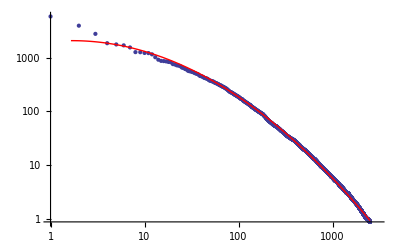

```mathematica
Show[
ListLogLogPlot[s⟦Range[1,2500]⟧,PlotRange->{{1,3000},Automatic}],
Plot[quad,{x,0.5,Log[2500]}, PlotStyle->Red]]
```

The form of the singular values is then (for k≈ 300)
	λ_k≈c k^-1.5
The spectral gap then has the form (we want the spectral gap to be close to 1, or the ratio of singular values close to zero)
	1-(λ_(k+1))/λ_k =1- (k/(k+1) )^1.5
which is a gastly slow rate.  We’d like for the spectral gap to be large.

```mathematica
gap[k_,δ_]:=1-(k/(k+δ))^1.5
```

The gap shrinks as k increases.

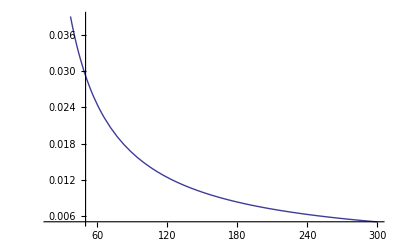

```mathematica
Plot[gap[k,1],{k,20,300}]
```

Thus, you have to get more separation at the higher singular vectors, such by making the separation in the gap δ proportional to k.

```mathematica
{gap[100,25],gap[200,50],gap[400,100]}
```

{0.284458,0.284458,0.284458}

Duh.  Pretty easy to see that the k cancels if δ is a multiple of k.

```mathematica
gap[k,k/4]
```

0.284458

Now the question becomes how much of the leading singular vectors u_kdo we get in the random projection.  This explains why the proportion increase in the spread, but not why 20/25% is enough to get 100% of e_kin the span of the leading random singular vectors.

## Normalizing Bigram Centroid Variables

This output shows why use use the symmtric normalization for the bigram matrix when constructing the predictors.  Looks nicer, takes out the Zipf pattern, but that’s not to say that its more predictive.

The SVD eigenwords of the bigram matrix are unrelated to word frequency.  These show the left eigenword SS for several forms of normalization of the bigram frequencies. All have equal SS.

The variance of the bigram variables drops off in Zipf form. These are variables formed as document centoids based on the eigenwords constructed from the bigram matrix.

The SS falls off just as the Zipf distribution of the words drops off.  We start with the eigenwords, but once form these centroids, the Zipf form shows up.

The source of this pattern is that the eigenwords are very much related to the word frequencies when the bigram matrix is not normalized.  The only way to approximate the bigram counts is to have the Zipf structure.  With symmetric normalization, the eigenwords reflect less of this gross overall structure.  The two left plots are the 4th eigenword squared components; the two on the right are the 450th.  There’s a bit of Zipf left after normalizing (ie, the squared weights are larger for the leading terms), but the magnitude is much reduced.

These plots show the benefit of normalizing.

The symmetric normalization leaves some of that present, but more benign.

Asymmetric normalization is weird, and either partially removes the effect but adds the weird cusp the unnormalized side.